# Completed Thesis Notebook

### Constants and Notation Initialization

#### Initialization

Mathematica will allow you to define and redefine a variable with a subscript and then it is locked in or “protected” as some definition(s) until the kernel is stopped and restarted. This prevents you from finding any symbolic expressions using that variable. To avoid restarting the kernel multiple times, we can use the functions below to make Mathematica consider certain subscripted variables to be malleable variables whose definitions can be changed and more importantly, cleared. They will now behave as any non-subscripted variable would.

```mathematica
Subscript[Test, bad]=7; (* Feel free to remove the semicolons and run this to see what I mean. *)
Clear[Subscript[Test, bad]]
Subscript[Test, bad];
ClearAll["Global`*"]
Subscript[Test, bad];
```

Every subscripted constant used in the thesis is initialized right here.

```mathematica
Needs["Notation`"]
Symbolize[ParsedBoxWrapper[SubscriptBox["k","sub"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["k","1"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["k","corr"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["k","initial"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["Rate","in"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["Rate","out"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["R","1"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["R","2"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["T","c"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["T","s"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["N","0"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["N","1"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["N","2"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["N",""]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["N","total"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["N","solve"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["PlotN","2"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["dN","2"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["n","thul"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["n","0"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["n","2"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["M","2"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["M","0"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["σ","e"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["σ","a"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["V","abs"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["P","abs"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["P","absN1"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["ℙ","0"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["τ","eff"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["τ","effP"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["τ","effcorr"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["γ","0"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["γ","eff"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["γ","effP"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["γ","effcorr"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["r","γ"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["r","γ0"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["r","γ01"]]]
Symbolize[ParsedBoxWrapper[SubscriptBox["T","final"]]]
```

#### Constants

This is a list of general variables used within the experiment.

```mathematica
μms=10^-6;
Subscript[k, corr]=7.844 10^-23;
Subscript[n, thul]=3 10^26;           (* Density of Thulium per meter *)
Subscript[γ, 0]=1/(480 10^-6);(* Decay Rate *)
r=5 10^-6;                (* Fiber Radius *)
area=Pi r^2.;
Gain=35.06;                   (* Refer to gain equation section *)
α=1.059;                         (* Absorption Coeff *)
l=2.15;                           (* Fiber length *)
Subscript[σ, e]=9. 10^-26 ;          (* Emission x Section *)
Subscript[σ, a]=2.8 10^-28;        (* Absorption x Section *)
CR=1.6;                         (* Cross Relaxation *)
Subscript[P, in]=1.89;
Subscript[P, out]=Subscript[P, in] E^(-α l);
Subscript[P, abs]=Subscript[P, in]-Subscript[P, out];                   
Subscript[P, absN1]=Subscript[P, abs] (1-Subscript[N, 2]/Subscript[N, total]);                       
hν=2.5 10^-19;       (* hv pump or average photon energy at the specified wavelength? *)
k=1.5 10^-23;       (* will be specifically Subscript[k, 1310] referenced from thesis and king&jackson pdf *)
𝕍=area l;
Subscript[V, abs]=area/α;             (* Absorption Volume *)
Γ=.75;                             (* Modal Overlap with Core*)
Subscript[N, total]=Subscript[n, thul] area l;
```

## Required Equations

## The Gain Equation

### Reminder of Constants/Reset Variables Checkpoint

Reminders of constants like this will be spaced out throughout the thesis for convenience.

```mathematica
ClearAll["Global`*"]
μms=10^-6;
Subscript[k, corr]=7.844 10^-23;
Subscript[n, thul]=3 10^26;
Subscript[γ, 0]=1/(480 10^-6);
r=5 10^-6; 
area=Pi r^2.;
𝕍=area l;
Gain=35.06;
α=1.059;
l=.1;
Subscript[σ, e]=9. 10^-26 ;
Subscript[σ, a]=2.8 10^-28; 
CR=1.6;
Clear[Subscript[N, 2]]
Subscript[P, in]=1.89;
Subscript[P, out]=Subscript[P, in] E^(-α l);
Subscript[P, abs]=Subscript[P, in]-Subscript[P, out];                   
Subscript[P, absN1]=Subscript[P, abs] (1-Subscript[N, 2]/Subscript[N, total]);
hν=2.5 10^-19;
k=1.5 10^-23; 
Subscript[V, abs]=area/α;
Γ=.75;
Subscript[N, total]=Subscript[n, thul] 𝕍;
```

### Gain Computation

```mathematica
ClearAll["Global`*"]
Subscript[N, 1]=Subscript[N, total]-Subscript[N, 2];Γ=.75;Subscript[σ, a]=2.8 10^-28;Subscript[σ, e]=9 10^-26;l=2.15;Subscript[N, total]=𝕍 Subscript[n, thul];r=5 10^-6;area=Pi r^2;𝕍=area l;
Subscript[n, thul]=3 10^26;Subscript[N, solve]=Solve[Log[Gain]==(2 Γ (Subscript[N, 2] Subscript[σ, e]-Subscript[N, 1] Subscript[σ, a]))/area,Subscript[N, 2]];
Gaintest=1/(Subscript[T, c]^2 Subscript[T, s]^4 Subscript[R, 1] Subscript[R, 2]);
Subscript[R, 1]=.997;
Subscript[R, 2]={.033,.50,.99}; (* Using .99 in case we use a high-reflecting mirror in the future *)
Subscript[T, c]=.95;
Subscript[T, s]=.99;
Clear[Gain]
Gaintest
Gain=Gaintest[[1]];
Subscript[N, 2]=(2 Subscript[N, total] Γ Subscript[σ, a]+area Log[Gaintest])/(2 Γ (Subscript[σ, a]+Subscript[σ, e]))
```

{35.0593,2.31391,1.16864}

{2.2201×10^15,6.43676×10^14,2.47499×10^14}

{{N_2→(2 N_total Γ σ_a+area Log[Gain])/(2 Γ (σ_a+σ_e))}}

Next, we will use this first-acquired value of Gain to use in a second equation that utilizes the Gain.

```mathematica
Clear[Subscript[N, 2]]
Subscript[N, solve]=Solve[Log[Gain]==(2 Γ (Subscript[N, 2] Subscript[σ, e]-Subscript[N, 1] Subscript[σ, a]))/area,Subscript[N, 2]]
l=2.15; (* You may need to change l in the checkpoint section for a change in l to prevent bugging *)
Subscript[N, 1]=Subscript[N, total]-Subscript[N, 2];Γ=.75;Subscript[σ, a]=2.8 10^-28;Subscript[σ, e]=9 10^-26;
Subscript[N, total]=Subscript[n, thul] 𝕍     (* Total # of Thulium Atoms in Fiber *)
Subscript[N, solve]=Solve[Log[Gain]==(2 Γ (Subscript[N, 2] Subscript[σ, e]-Subscript[N, 1] Subscript[σ, a]))/area,Subscript[N, 2]]
Subscript[N, 2]=Subscript[N, solve][[1,1,2]](* Mtmatica replaces Subscript[N, 1] with Subscript[N, total] - Subscript[N, 2] to compute *)
PercentForm[Subscript[N, 2]/Subscript[N, total]]
Solve[Subscript[N, 2]==Subscript[n, 0] area ∫_0^l ⅇ^(-α z)ⅆz,Subscript[n, 0]]
```

{{N_2→2.07029×10^15}}

5.06582×10^16

{{N_2→2.07029×10^15}}

2.07029×10^15

4.087%

{{n_0→3.11068×10^25}}

Since the k value and emission cross section values aren’t very reliable we need another way to try and find N_2. More on this in the Rate Equations section.

#### Modelling The Effect of Different Output Couplers on Laser Performance or N_2

```mathematica
ClearAll["Global`*"]
Gainsolve=Solve[Log[Gain]==(2 Γ (Subscript[N, 2] Subscript[σ, e]-Subscript[N, 1] Subscript[σ, a]))/area,Subscript[N, 2]]
Γ=.75;Subscript[σ, a]=2.8/10^28;Subscript[σ, e]=9/10^26;l=.1;r=5/10^6;area=π r^2;
Subscript[R, 1]=.997;Subscript[R, 2]={.033,.50,.99};Subscript[T, c]=.95;Subscript[T, s]=.99;Gaintest=1/(Subscript[T, c]^2 Subscript[T, s]^4 Subscript[R, 1] Subscript[R, 2]);
Gain=Gaintest⟦{1,2,3}⟧
Subscript[N, 2]=Gainsolve⟦1,1,2⟧
```

{{N_2→(-(4.71239×10^15 Γ σ_a)/area-Log[Gain])/(-(2. Γ σ_a)/area-(2. Γ σ_e)/area)}}

{35.0593,2.31391,1.16864}

{2.07029×10^15,4.93869×10^14,9.76921×10^13}

## The Rate Equations

#### Reminder of Constants/Reset Variables Checkpoint

```mathematica
ClearAll["Global`*"]
μms=10^-6;
Subscript[k, corr]=7.844 10^-23;
Subscript[n, thul]=3 10^26;
Subscript[γ, 0]=1/(480 10^-6);
r=5 10^-6; 
area=Pi r^2.;
𝕍=area l;
Gain=35.06;
α=1.059;
l=.1;
Subscript[σ, e]=9. 10^-26 ;
Subscript[σ, a]=2.8 10^-28; 
CR=1.6;
Clear[Subscript[N, 2]]
Subscript[P, in]=1.89;
Subscript[P, out]=Subscript[P, in] E^(-α l);
Subscript[P, abs]=Subscript[P, in]-Subscript[P, out];                   
Subscript[P, absN1]=Subscript[P, abs] (1-Subscript[N, 2]/Subscript[N, total]);
hν=2.5 10^-19;
k=1.5 10^-23; 
Subscript[V, abs]=area/α;
Γ=.75;
Subscript[N, total]=Subscript[n, thul] 𝕍;
```

#### Computation of N_2 (aka, N_0 @ time t=0) With Literature Value of k

```mathematica
ClearAll["Global`*"];
CR=1.6;l=.1; (* Length of 10 cm to make assumptive calculations more accurate *)
Subscript[n, thul]=3 10^26;Subscript[N, total]=Subscript[n, thul] 𝕍;
r=5 10^-6;area=Pi r^2;𝕍=area l;hν=2.5/10^19;k=1.5/10^23;
Subscript[γ, 0]=1/(480 10^-6);
α=1.059;
Subscript[P, in]=1.89;
Subscript[P, out]=Subscript[P, in] E^(-α l);
Subscript[P, abs]=Subscript[P, in]-Subscript[P, out];
Subscript[P, absN1]=Subscript[P, abs] (1-Subscript[N, 2]/Subscript[N, total]); (* This was a correction factor for Subscript[P, abs] derived by Dr. Shiner. Further iteration wasn't necessary because the singularity point (for lack of a better term) was reached after only one iteration of the correction. *)
Subscript[Rate, in]=(CR Subscript[P, absN1])/hν;Subscript[Rate, out]=Subscript[γ, 0] Subscript[N, 2]+(2 k Subscript[N, 2]^2)/𝕍; 
(* The general rate equation from the thesis will have what I define as Subscript[Rate, in] and Subscript[Rate, out] to be equal to one another *)
T1=Solve[Subscript[Rate, in]==Subscript[Rate, out],Subscript[N, 2]];
Subscript[N, 2]=T1⟦2,1,2⟧ (* Subscript[N, 0] @ time t=0 for future reference *)
PercentForm[Subscript[N, 2]/Subscript[N, total]]
Subscript[P, absN1]
Subscript[τ, eff]=Subscript[N, 2]/Subscript[Rate, in](* Should come out to 303 μs *)
```

3.18529×10^14

13.52%

0.164243

0.000303028

I expect that with the first two sections of the equation set equal to one another, all three should have the same value if expressed by their lonesome. 
This is because the chosen literature k value of 1.5 x 10^-23 forced out an N_2 that created an equilibrium between all the parts of the equation.

```mathematica
k
(CR Subscript[P, absN1])/hν (* This is the LHS of eqn 4 *)
Subscript[N, 2]/Subscript[τ, eff](* Simplified RHS of eqn 4 *)
Subscript[γ, 0] Subscript[N, 2]+(2 k Subscript[N, 2]^2)/𝕍 (* Middle of eqn 4 *)
```

1.5×10^-23

1.05115×10^18

1.05115×10^18

1.05115×10^18

#### Solving for Corrected k

We suspect that the correct k value is actually about 5x larger than the literature k.

```mathematica
Clear[Subscript[N, 2]];CR=1.6;l=.1;Subscript[n, thul]=3 10^26;r=5 10^-6;area=Pi r^2;𝕍=area l;hν=2.5/10^19;k=7.844/10^23;Subscript[N, total]=Subscript[n, thul] 𝕍;
Subscript[γ, 0]=1/(480 10^-6);
α=1.059;
Subscript[V, abs]=area/α;
Subscript[P, in]=1.89;
Subscript[P, out]=Subscript[P, in] E^(-α l);
Subscript[P, abs]=Subscript[P, in]-Subscript[P, out]
Subscript[P, absN1]=Subscript[P, abs] (1-Subscript[N, 2]/Subscript[N, total]);
Subscript[Rate, in]=(CR Subscript[P, absN1])/hν;Subscript[Rate, out]=Subscript[γ, 0] Subscript[N, 2]+(2 k Subscript[N, 2]^2)/𝕍;
T1=Solve[Subscript[Rate, in]==Subscript[Rate, out],Subscript[N, 2]];
Subscript[N, 2]=T1⟦2,1,2⟧ (* Subscript[N, 0] @ time t=0 for future reference *)
PercentForm[Subscript[N, 2]/Subscript[N, total]]
Subscript[P, absN1]
Subscript[τ, eff]=ScientificForm[Subscript[N, 2]/Subscript[Rate, in]] (* Should come out to 170 μs *)
```

0.189917

1.90053×10^14

8.066%

0.174598

1.70081×10^-4

```mathematica
Subscript[τ, eff]=1/((2 k Subscript[N, 2])/𝕍+Subscript[γ, 0])
(CR Subscript[P, absN1])/hν (* This is the LHS of eqn 4 *)
Subscript[N, 2]/Subscript[τ, eff]  (* Simplified RHS of eqn 4 *)
Subscript[γ, 0] Subscript[N, 2]+(2 k Subscript[N, 2]^2)/𝕍 (* Middle of eqn 4 *)
```

0.000170204

1.11736×10^18

1.11736×10^18

1.11736×10^18

All three are supposed to match. The best way to make them match is to change k.

## Changing k, Realizing Its Effects on N_2 and γ_0

### Reminder of Constants

```mathematica
ClearAll["Global`*"]
Subscript[k, corr]=7.844 10^-23;
Subscript[n, thul]=3 10^26;
Subscript[γ, 0]=1/(480 10^-6);
r=5 10^-6; 
area=Pi r^2.;
𝕍=area l;
Gain=35.06;
α=1.059;
l=.1; (* We use 10 cm here to simplify calculations. This utilized a linear slope rather than an exponential one *)
Subscript[σ, e]=9. 10^-26 ;
Subscript[σ, a]=2.8 10^-28; 
CR=1.6;
Clear[Subscript[N, 2]]
Subscript[P, in]=1.89;
Subscript[P, out]=Subscript[P, in] E^(-α l);
Subscript[P, abs]=Subscript[P, in]-Subscript[P, out];                   
Subscript[P, absN1]=Subscript[P, abs] (1-Subscript[N, 2]/Subscript[N, total]);
hν=2.5 10^-19;
k=1.5 10^-23; 
Subscript[V, abs]=area/α;
Γ=.75;
Subscript[N, total]=Subscript[n, thul] 𝕍;
```

### k Changes & Computation

Let us vary the k value around a little bit. Near the bottom of this section, we will see that γ_eff = γ_0 when k = 0. The decay rate and lifetime each have a dependency on both k and N_2. And N_2 has its own dependency on k. So we need a function that automatically adjusts N_2 for each change made to k.

We know that N_2 depends on what we make k equal to. So we will make a plot of the N_2 values as k changes.

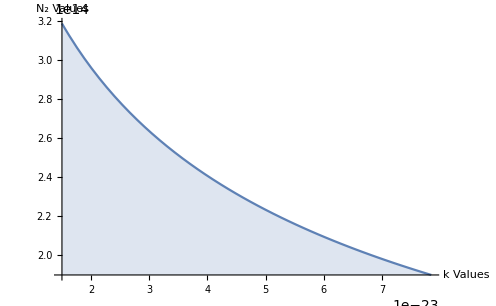

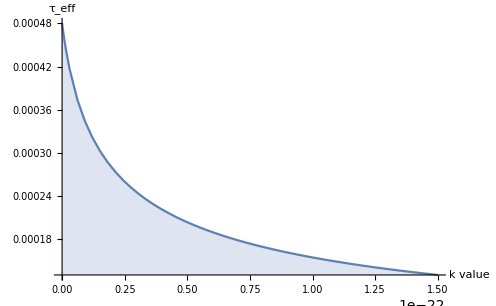

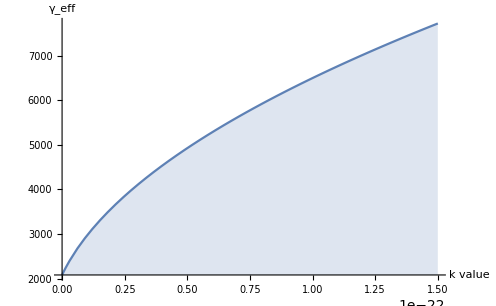

```mathematica
ClearAll["Global`*"]
Subscript[P, absN1]=Subscript[P, abs] (1-Subscript[N, 2]/Subscript[N, total]);Subscript[Rate, in]=(CR Subscript[P, absN1])/hν;Subscript[Rate, out]=Subscript[γ, 0] Subscript[N, 2]+(2 k Subscript[N, 2]^2)/𝕍; T1=Simplify[Solve[Subscript[Rate, in]==Subscript[Rate, out],Subscript[N, 2]]] ;
(* I will copy and paste the first value of T1 as our definition for Subscript[N, 2] after a couple more lines becuase Subscript[N, 2] needs to be a positive value. I used a semicolon to hide the result of T1, as it is quite large. *)
CR=1.6;l=.1;Subscript[n, thul]=3 10^26;Subscript[N, total]=Subscript[n, thul] 𝕍;r=5 10^-6;area=Pi r^2;𝕍=area l;hν=2.5/10^19;
Subscript[γ, 0]=1/(480 10^-6);α=1.059;Subscript[P, in]=1.89;Subscript[P, out]=Subscript[P, in] E^(-α l);Subscript[P, abs]=Subscript[P, in]-Subscript[P, out];Subscript[k, initial]=1.5 10^-23;


Subscript[N, 2]=T1[[1,1,2]]; (* You can test out the second (negative) value by using 2 instead of 1 for the first number in the brackets *)
Plot[Subscript[N, 2],{k,1.5 10^-23,7.844 10^-23},AxesLabel->{"k Values","N_2 Values"},Filling->Bottom]

Subscript[τ, eff]=Subscript[N, 2] (Subscript[γ, 0] Subscript[N, 2]+2 k Subscript[N, 2]^2 𝕍^-1)^-1;
Plot[Subscript[τ, eff],{k,0,10 Subscript[k, initial]},AxesLabel->{"k value","τ_eff"},Filling->Bottom]

Subscript[γ, eff]=1/Subscript[τ, eff];
Plot[Subscript[γ, eff],{k,0,10 Subscript[k, initial]},AxesLabel->{"k value","γ_eff"},Filling->Bottom]
```

As we can see in our plot above, N_2 decreases as k increases.

We find that larger values of k result in a larger excited state population, along with a shorter excited state lifetime.

## Differentiation of N_2 With Respect to Time(t)

## Main Equation With Increasing Intricacy Level

Here, we are creating a differential equation from our already established equation Rate_out=γ_0 N_2+(2 k N_2^2)/𝕍 = N_2(γ_0 +(2 k N_2)/𝕍). This form can be extremely simplified by getting rid of the constants. This helps us to check our process by hand, as doing the full equation’s process by hand takes up a lot of space and time. When simplified, the expression looks like  N_2(1 +N_2). Below are equations that are based on steps from doing the basic expression by hand. The more complete and intricate versions of this equation follow the same exact steps as the basic one, just with new constants thrown in. “Proof” is essentially the formula for doing this differential equation at its core. You just need to add in the constants described below as you increase the intricacy level.

```mathematica
ClearAll["Global`*"]
BaseEqn=ℕ[t] (1+ℕ[t]); (* Subscript[N, 2] will be notated as ℕ[t] for calculation purposes in this section. *)
T1=DSolve[ℕ'[t]==-ℕ[t] (1+ℕ[t]),ℕ[t],t];(* Start with this basic equation and check by hand if desired *)
T2=DSolve[ℕ'[t]==-ℕ[t] (1+k ℕ[t]),ℕ[t],t]; (* Add a k to "Proof" below. Multiply it by the second Num[[level]] *)
T3=DSolve[ℕ'[t]==-ℕ[t] (γ+k ℕ[t]),ℕ[t],t]; (* Add a γ to "Proof" below. Multiply it by the "Den[[level]]" in the numerator *)
T4=DSolve[ℕ'[t]==-ℕ[t] (γ+(2 k ℕ[t])/𝕍),ℕ[t],t];(* Add a 2/𝕍 to "Proof" below. Multiply this by the k you put in earlier *)
Nn=Simplify[T4⟦1,1,2⟧]; (* Change this to T1,T2,T3, or T4, as you need to *)
dNn=D[Nn, t]
Num={ⅇ^C1,ⅇ^C1,ⅇ^(γ C1) γ,ⅇ^(𝕍 γ C[1]) 𝕍 γ};Den={ⅇ^t-ⅇ^C1,ⅇ^t-ⅇ^C1 k,ⅇ^(t γ)-ⅇ^(γ C1) k,ⅇ^(t γ)-2 ⅇ^(𝕍 γ C[1]) k};
level=4;(* Make sure this corresponds to "Nn" and add the variables needed to "Proof" for each level *)
Proof=Simplify[-(Num⟦level⟧ (Den⟦level⟧ γ +2 k/𝕍 Num⟦level⟧))/(Den⟦level⟧ Den⟦level⟧)] (* Remember at level 1 there's a + sign in (Den[[level]] + Num[[level]] *)
```

-(ⅇ^(t γ+𝕍 γ C[1]) 𝕍 γ^2)/((ⅇ^(t γ)-2 ⅇ^(𝕍 γ C[1]) k)^2)

-(ⅇ^(γ (t+𝕍 C[1])) 𝕍 γ^2)/((ⅇ^(t γ)-2 ⅇ^(𝕍 γ C[1]) k)^2)

## Introducing Dummy Variable A to Replace c_1. Get Expression in Terms of N_0.

N_0 will be denoted in this section as N0 and represents the number of excited state atoms at time t = 0. We can take our N_0 found from earlier to get an official value for N_0, but plug it in at the end of this section. First I will display another system of equations for variable A in increasing complexity. The general idea is for us to replace e^c1 or anything that has c1 in it with variable A and then solve the system for A in terms of N0. This way the whole equation is void of the pesky c1 integration constant with N0 being  simple to compute. Similar to the last section, this one will have increasing levels of intricacy or completeness of the equation.

#### A for T1

```mathematica
ClearAll["Global`*"]
BaseEqn=ℕ[t] (1+ℕ[t]);
T1=DSolve[ℕ'[t]==-ℕ[t] (1+ℕ[t]),ℕ[t],t] (* Use basic equation *)
ℕ[t]=Simplify[T1⟦1,1,2⟧] (* We'll take ⅇ^C[1] and turn it into the constant 𝔸 *)
FindA=Solve[Subscript[N, 0]==𝔸/(1-𝔸),𝔸];𝔸=FindA[[1,1,2]](* Subscript[N, 0] is for time(t) = 0 *)
ℕ[t]=Simplify[𝔸/(1-𝔸)]
```

{{ℕ[t]→-ⅇ^C[1]/(-ⅇ^t+ⅇ^C[1])}}

ⅇ^C[1]/(ⅇ^t-ⅇ^C[1])

N_0/(1+N_0)

N_0

#### A for T2

```mathematica
ClearAll["Global`*"]
BaseEqn=ℕ[t] (1+ℕ[t]);
T2=DSolve[ℕ'[t]==-ℕ[t] (1+k ℕ[t]),ℕ[t],t];ℕ[t]=Simplify[T2⟦1,1,2⟧]
FindA=Solve[Subscript[N, 0]==𝔸/(1-𝔸 k),𝔸];𝔸=FindA[[1,1,2]]
ℕ[t]=Simplify[𝔸/(ⅇ^t-𝔸 k)]
```

ⅇ^C[1]/(ⅇ^t-ⅇ^C[1] k)

N_0/(1+k N_0)

N_0/(-k N_0+ⅇ^t (1+k N_0))

#### A for T3

```mathematica
ClearAll["Global`*"]
BaseEqn=ℕ[t] (1+ℕ[t]);
T3=DSolve[ℕ'[t]==-ℕ[t] (γ+k ℕ[t]),ℕ[t],t];ℕ[t]=Simplify[T3⟦1,1,2⟧]
FindA=Solve[Subscript[N, 0]==(𝔸 γ)/(1-𝔸 k),𝔸];𝔸=FindA[[1,1,2]]
ℕ[t]=Simplify[(𝔸 γ)/(ⅇ^(t γ)-𝔸 k)]
```

(ⅇ^(γ C[1]) γ)/(ⅇ^(t γ)-ⅇ^(γ C[1]) k)

N_0/(k N_0+γ)

(N_0 γ)/((-1+ⅇ^(t γ)) k N_0+ⅇ^(t γ) γ)

We can see here that our expression for N[t] is becoming more intricate as we make our base equation more and more complete. Doing this full equation by hand would prove to be heavily error prone and tedious.

#### A for T_final

```mathematica
ClearAll["Global`*"]
Subscript[T, final]=DSolve[ℕ'[t]==-ℕ[t] (γ+(2 k ℕ[t])/𝕍),ℕ[t],t];
ℕ[t]=Simplify[Subscript[T, final]⟦1,1,2⟧] (* Remember, we take each ⅇ^(𝕍 γ C[1]) from this answer and replace it with A. This creates our next line *)
```

(ⅇ^(𝕍 γ C[1]) 𝕍 γ)/(ⅇ^(t γ)-2 ⅇ^(𝕍 γ C[1]) k)

```mathematica
FindA=Solve[Subscript[N, 0]==(𝔸 γ 𝕍)/(1-2 𝔸 k),𝔸]; 𝔸=FindA⟦1,1,2⟧
ℕ[t]=(𝔸 𝕍 γ)/(ⅇ^(t γ)-2 𝔸 k) 
Simplify[ℕ[t]]
```

N_0/(2 k N_0+𝕍 γ)

(N_0 𝕍 γ)/((2 k N_0+𝕍 γ) (ⅇ^(t γ)-(2 k N_0)/(2 k N_0+𝕍 γ)))

(N_0 𝕍 γ)/(2 (-1+ⅇ^(t γ)) k N_0+ⅇ^(t γ) 𝕍 γ)

#### Simplifying Our Final Result of N_2

ℕ[t] is a little hard to work with right now despite being simplified, so we’ll work on simplifying it further. First of all, I’ll expand the denominator.

```mathematica
(N0 𝕍 γ)/(-2 k N0+2 k N0 ⅇ^(t γ)+ⅇ^(t γ) 𝕍 γ);
```

This expression for ℕ[t] is still unwieldy. We’ll throw an ⅇ^(-γ_0t)/ⅇ^(-γ_0t) in and multiply everything by that.

```mathematica
Subscript[N, 2]=(Subscript[N, 0] ⅇ^(-Subscript[γ, 0] t) 𝕍 γ)/(-2 ⅇ^(-Subscript[γ, 0] t) k Subscript[N, 0]+2 k Subscript[N, 0]+𝕍 γ);(* Now I'll divide out a (𝕍 Subscript[γ, 0])/(𝕍 Subscript[γ, 0]) from the equation *)
Subscript[N, 2]=(Subscript[N, 0] ⅇ^(-Subscript[γ, 0] t))/(-(2 ⅇ^(-Subscript[γ, 0] t) k Subscript[N, 0])/(𝕍 γ)+(2 k Subscript[N, 0])/(𝕍 γ) +1);
```

At this point, we have a form of the equation that seems bad, but we’ll define a new variable r. r will represent the following variables in our equation.

```mathematica
r=(2 k Subscript[N, 0])/(Subscript[γ, 0] 𝕍);Subscript[N, 2]=(Subscript[N, 0] ⅇ^(-Subscript[γ, 0] t))/(-(2 ⅇ^(-Subscript[γ, 0] t) k Subscript[N, 0])/(𝕍 γ)+(2 k Subscript[N, 0])/(𝕍 γ) +1);
(* try plugging r into the equation for what it represents and you'll find a new much simpler equation *)
Subscript[N, 2]=(Subscript[N, 0] ⅇ^(-Subscript[γ, 0] t))/(-r ⅇ^(-Subscript[γ, 0] t)+r +1);Subscript[N, 2]=(Subscript[N, 0] ⅇ^(-Subscript[γ, 0] t))/(1+r (1-ⅇ^(-Subscript[γ, 0] t)));
```

So this is our current form for N_2. This will be utilized heavily in the final sections of this experiment. The r term will prove helpful in maintaining a semblance of simplicity in here.

## Implementing The Ratios

#### The Algebra

In this section I utilize r and begin looking for the Power output (or luminescence) of the laser and it’s relation to N_2 after time(t). I introduce the initial power ℙ_0 for when the laser turns off. This term is very different from N_2 itself, yet very similar in terms of its rate of decay. The only difference between the two is a multiplicative constant k_1 that makes ℙ_0 and later power outputs generally smaller than N_2 at any point in time.

```mathematica
ClearAll["Global`*"]
r=(2 k Subscript[N, 0])/(Subscript[γ, 0] 𝕍);Subscript[N, 2]=(Subscript[N, 0] ⅇ^(-Subscript[γ, 0] t))/(1+r (1-ⅇ^(-Subscript[γ, 0] t)));
Subscript[dN, 2]=Simplify[D[Subscript[N, 2],t]]; (* The derivative of Subscript[N, 2] with respect to t *)
Subscript[ℙ, 0]=Simplify[Subscript[k, 1] (Subscript[γ, 0] Subscript[N, 2]+(2 k Subscript[N, 2]^2)/𝕍)]
Simplify[(Subscript[γ, 0] Subscript[N, 2]+(2 k Subscript[N, 2]^2)/𝕍)] (* Notice that this is simply the original equation for the rate out of the excited state. Subscript[P, 0] is exactly this equation, but with its Subscript[k, 1] corrective coefficient. *)
Simplify[Subscript[dN, 2]]
```

(ⅇ^(t γ_0) k_1 N_0 𝕍 γ_0^2 (2 k N_0+𝕍 γ_0))/((2 (-1+ⅇ^(t γ_0)) k N_0+ⅇ^(t γ_0) 𝕍 γ_0)^2)

(ⅇ^(t γ_0) N_0 𝕍 γ_0^2 (2 k N_0+𝕍 γ_0))/((2 (-1+ⅇ^(t γ_0)) k N_0+ⅇ^(t γ_0) 𝕍 γ_0)^2)

-(ⅇ^(t γ_0) N_0 𝕍 γ_0^2 (2 k N_0+𝕍 γ_0))/((2 (-1+ⅇ^(t γ_0)) k N_0+ⅇ^(t γ_0) 𝕍 γ_0)^2)

You might be wondering why the last result has a negative and the other two answers don’t have one. This is because the first two values are magnitudes of the rate at which N_2 is decreasing or the rate at which Power is decreasing. These two values are inherently represent decreasing functions, so it’s good that they are positive. Otherwise, with a negative in front of them, they would both actually represent a positive function. The last output shows the change in these decreases. The rate of these function slows down, and this is denoted by that negative sign that you see in front of the function.

#### The Graphs for The Algebra

Let' s start working into some plots so we can visualize all this algebra . Nt is going to be used instead of N[t] for this section .

```mathematica
ClearAll["Global`*"]
Subscript[r, γ]=(2 k Subscript[N, 0])/(γ 𝕍);r=(2 k Subscript[N, 0])/(γ 𝕍);Nt=Simplify[Subscript[N, 0]/(ⅇ^(t γ) (1+Subscript[r, γ])-Subscript[r, γ])];Simplify[D[Nt, t]]
k=1.5/10^23;γ=1/(480 10^-6);Subscript[N, 0]=3.18 10^14;𝕍=.1 π (5/10^6)^2;
Nt2=Subscript[N, 0] ⅇ^(-γ t);
Simplify[%/(Subscript[N, 0] γ)];
Simplify[D[Nt, t]]
Plot[{Nt,Nt2},{t,0,10^-3},AxesLabel->{"Time(t)","N_2 State Population"},PlotLabels->Automatic]
Plot[{Nt/Subscript[N, 0],Nt2/Subscript[N, 0]},{t,0,10^-3},AxesLabel->{"Time(t)","N_2 State Population"},PlotLabels->{"Nt/N_0","Nt2/N_0"}]
Plot[{Log[Nt/Subscript[N, 0]],Log[Nt2/Subscript[N, 0]]},{t,0,10^-3},AxesLabel->{"Time(t)","N_2 State Population"},PlotLabels->{"Log[Nt/N_0]","Log[Nt2/N_0]"}]
```

-(ⅇ^(t γ) N_0 𝕍 γ^2 (2 k N_0+𝕍 γ))/((2 (-1+ⅇ^(t γ)) k N_0+ⅇ^(t γ) 𝕍 γ)^2)

-(4.18498×10^17 ⅇ^(6250 t/3))/((0.368305-1. ⅇ^(6250 t/3))^2)

-Graphics-

-Graphics-

-Graphics-

#### Finding P_0

```mathematica
ClearAll["Global`*"]
r=(2 k Subscript[N, 0])/(Subscript[γ, 0] 𝕍);Subscript[N, 2]=(Subscript[N, 0] ⅇ^(-Subscript[γ, 0] t))/(1+r (1-ⅇ^(-Subscript[γ, 0] t)))
Subscript[dN, 2]=Simplify[D[Subscript[N, 2],t]]
Subscript[ℙ, 0]=Simplify[Subscript[k, 1] (Subscript[γ, 0] Subscript[N, 2]+(2 k Subscript[N, 2]^2)/𝕍)]
Subscript[N, 0]=3.185 10^14;t=0;Subscript[γ, 0]=1/(480 10^-6);k=1.5 10^-23;l=.1;r=5 10^-6;area=Pi r^2;𝕍=area l;α=1.059;
Subscript[P, in]=1.89;(* This is the Subscript[P, in] that was experimentallyt found/used *)
Subscript[ℙ, 0]
```

(ⅇ^(-t γ_0) N_0)/(1+(2 (1-ⅇ^(-t γ_0)) k N_0)/(𝕍 γ_0))

-(ⅇ^(t γ_0) N_0 𝕍 γ_0^2 (2 k N_0+𝕍 γ_0))/((2 (-1+ⅇ^(t γ_0)) k N_0+ⅇ^(t γ_0) 𝕍 γ_0)^2)

(ⅇ^(t γ_0) k_1 N_0 𝕍 γ_0^2 (2 k N_0+𝕍 γ_0))/((2 (-1+ⅇ^(t γ_0)) k N_0+ⅇ^(t γ_0) 𝕍 γ_0)^2)

1.05102×10^18 k_1

#### Putting k_1 in terms of P_0 to then calculate P[t]

From last section we know that  P_0=1.051(10^18) k1 so we can algebraically find k1 in terms of P_0.

```mathematica
ClearAll["Global`*"]
r=(2 k Subscript[N, 0])/(Subscript[γ, 0] 𝕍);Subscript[N, 2]=(Subscript[N, 0] ⅇ^(-Subscript[γ, 0] t))/(1-r (1-ⅇ^(-Subscript[γ, 0] t)));Subscript[dN, 2]=Simplify[D[Subscript[N, 2], t]]
Subscript[N, 0]=3.185 10^14;Subscript[γ, 0]=1/(480 10^-6);k=1.5 10^-23;l=.1;r=5 10^-6;area=Pi r^2;𝕍=area l;α=1.059;
Subscript[k, 1]=Subscript[ℙ, 0]/(1.05102 10^18);
t=2/10^20;
Subscript[P, out]=Subscript[P, in] ⅇ^(-α l) (* Subscript[P, out] = Subscript[ℙ, 0]. Subscript[P, out] was found earlier within the notebook. *)
P[t]=Subscript[k, 1] Subscript[dN, 2];
Subscript[ℙ, 0]=1.7;
P[t]
Subscript[k, 1]
```

-(ⅇ^(t γ_0) N_0 𝕍 γ_0^2 (-2 k N_0+𝕍 γ_0))/((-2 (-1+ⅇ^(t γ_0)) k N_0+ⅇ^(t γ_0) 𝕍 γ_0)^2)

1.70008

-0.446522

1.61748×10^-18

This value of k_1 won’t actually be used past this point, and isn’t related to our k constant for the main equation.

## Using ∂N_2/∂t and ∂P/∂t to find τ_eff

## N_2 and Power Plots Over time t + k Constant Variation

### N_2 Plot Over Time

With all that we’ve done, we can now measure N_2 with a dependence on k and time(t) using our final equation.

(N_0 𝕍 γ_0)/(2 (-1+ⅇ^(t γ_0)) k N_0+ⅇ^(t γ_0) 𝕍 γ_0)

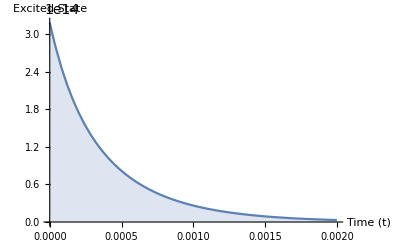

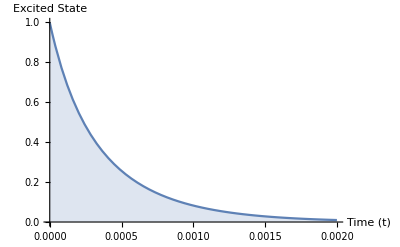

```mathematica
ClearAll["Global`*"]
Subscript[r, γ]=(2 k Subscript[N, 0])/(Subscript[γ, 0] 𝕍);Subscript[N, 2]=Simplify[(Subscript[N, 0] ⅇ^(-Subscript[γ, 0] t))/(1+Subscript[r, γ] (1-ⅇ^(-Subscript[γ, 0] t)))]
Pt=(Subscript[ℙ, 0] (Subscript[γ, 0] Subscript[N, 2]+(2 k Subscript[N, 2]^2)/𝕍))/(Subscript[γ, 0] Subscript[N, 0]+(2 k Subscript[N, 0]^2)/𝕍);τeff=(1+2 Subscript[r, γ])/(1+Subscript[r, γ]);dNt=D[Subscript[N, 2],t];
Subscript[N, 0]=3.185 10^14;Subscript[γ, 0]=1/(480 10^-6);k=1.5/10^23;l=.1;r=5/10^6;area=π r^2;𝕍=area l;α=1.059;Subscript[k, corr]=7.844/10^23;
Subscript[P, in]=1.89;Subscript[ℙ, 0]=Subscript[P, in] ⅇ^(-α l);
Plot[Subscript[N, 2],{t,0,2/10^3},Filling->Bottom,AxesLabel->{"Time (t)","Excited State"}]
Plot[Subscript[N, 2]/Subscript[N, 0],{t,0,2/10^3},Filling->Bottom,AxesLabel->{"Time (t)","Excited State"}](* Excited population in comparison to Subscript[N, 0], which is why this one starts at 1 *)
```

### Plotting Powers

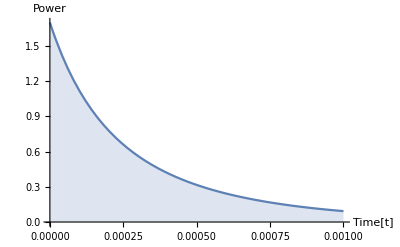

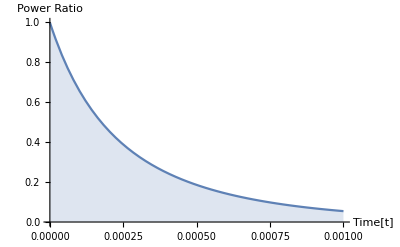

```mathematica
ClearAll["Global`*"]
Subscript[r, γ]=(2 k Subscript[N, 0])/(Subscript[γ, 0] 𝕍);Subscript[N, 2]=Simplify[(Subscript[N, 0] ⅇ^(-Subscript[γ, 0] t))/(1+Subscript[r, γ] (1-ⅇ^(-Subscript[γ, 0] t)))];Pt=(Subscript[ℙ, 0] (Subscript[γ, 0] Subscript[N, 2]+(2 k Subscript[N, 2]^2)/𝕍))/(Subscript[γ, 0] Subscript[N, 0]+(2 k Subscript[N, 0]^2)/𝕍);Subscript[r, γ]=(2 k Subscript[N, 0])/(Subscript[γ, 0] 𝕍);τeff=(1+2 Subscript[r, γ])/(1+Subscript[r, γ]);dNt=D[Subscript[N, 2],t];
Subscript[N, 0]=3.185 10^14;Subscript[γ, 0]=1/(480/10^6);k=1.5/10^23;l=.1;r=5/10^6;area=π r^2;𝕍=area l;α=1.059;Subscript[k, corr]=7.844/10^23;
Subscript[P, in]=1.89;Subscript[ℙ, 0]=Subscript[P, in] ⅇ^(-α l);
Plot[Pt,{t,0,1/10^3},Filling->Bottom,AxesLabel->{"Time[t]","Power"}]
Plot[Pt/Subscript[ℙ, 0],{t,0,1/10^3},Filling->Bottom,AxesLabel->{"Time[t]","Power Ratio"}](* A ratio just like the Subscript[N, 2] version above *)
```

## Powers Throughout Multiple k With Respect To Time

The graphs will become more intricate, but also more descriptive in this part. Most of the constants you’ve been seeing will remain the same though.

(-2.62562×10^17+7.12188×10^17 ⅇ^(6250 t/3)+1.75042×10^40 k1)/((0.36867-1. ⅇ^(6250 t/3))^2 (6.63542×10^17+2.58321×10^40 k1))

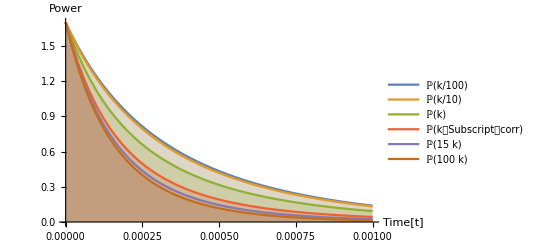

(-1.54441×10^17+4.18914×10^17 ⅇ^(6250 t/3)+1.02961×10^40 k1)/((0.36867-1. ⅇ^(6250 t/3))^2 (6.63542×10^17+2.58321×10^40 k1))

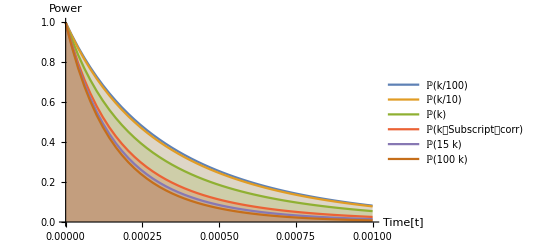

```mathematica
ClearAll["Global`*"]
Subscript[r, γ]=(2 k Subscript[N, 0])/(Subscript[γ, 0] 𝕍);Subscript[N, 2]=Simplify[(Subscript[N, 0] ⅇ^(-Subscript[γ, 0] t))/(1+Subscript[r, γ] (1-ⅇ^(-Subscript[γ, 0] t)))];Pt=(Subscript[ℙ, 0] (Subscript[γ, 0] Subscript[N, 2]+(2 k Subscript[N, 2]^2)/𝕍))/(Subscript[γ, 0] Subscript[N, 0]+(2 k Subscript[N, 0]^2)/𝕍);Subscript[r, γ]=(2 k Subscript[N, 0])/(Subscript[γ, 0] 𝕍);τeff=(1+2 Subscript[r, γ])/(1+Subscript[r, γ]);dNt=D[Subscript[N, 2],t];
Subscript[N, 0]=3.185 10^14;Subscript[γ, 0]=1/(480/10^6);k=1.5/10^23;l=.1;r=5/10^6;area=π r^2;𝕍=area l;α=1.059;Subscript[k, corr]=7.844/10^23;
Subscript[P, in]=1.89;Subscript[ℙ, 0]=Subscript[P, in] ⅇ^(-α l);
ℙ[k1_]=Simplify[(Subscript[ℙ, 0] (Subscript[γ, 0] Subscript[N, 2]+(2 k1 Subscript[N, 2]^2)/𝕍))/(Subscript[γ, 0] Subscript[N, 0]+(2 k1 Subscript[N, 0]^2)/𝕍)](* Equation for luminescent power output with respect to time(t) after the source is turned off *)
Plot[{ℙ[k/100],ℙ[k/10],ℙ[k],ℙ[Subscript[k, corr]],ℙ[15 k],ℙ[100 k]},{t,0,1/10^3},AxesLabel->{"Time[t]","Power"},PlotLegends->"Expressions",Filling->Bottom]
ℙ[k1_]=Simplify[(Subscript[ℙ, 0] (Subscript[γ, 0] Subscript[N, 2]+(2 k1 Subscript[N, 2]^2)/𝕍))/((Subscript[γ, 0] Subscript[N, 0]+(2 k1 Subscript[N, 0]^2)/𝕍) Subscript[ℙ, 0])](* Ratio version of the first luminescent power output *)
Plot[{ℙ[k/100],ℙ[k/10],ℙ[k],ℙ[Subscript[k, corr]],ℙ[15 k],ℙ[100 k]},{t,0,1/10^3},AxesLabel->{"Time[t]","Power"},PlotLegends->"Expressions",Filling->Bottom]
```

## Plotting N and P With Respect to Time + 2 Main k Values ***Iterate k up to 10 (k) ***

Here, we will use k_sub to set up a system where we can sketch plots and choose between using the literature k or our corrected k with ease.

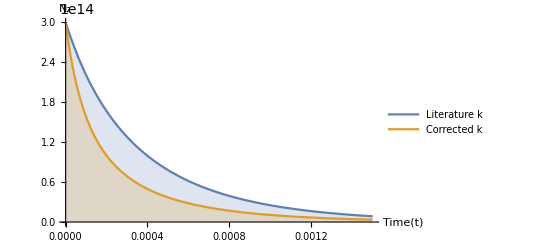

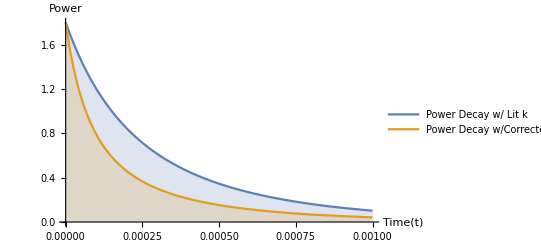

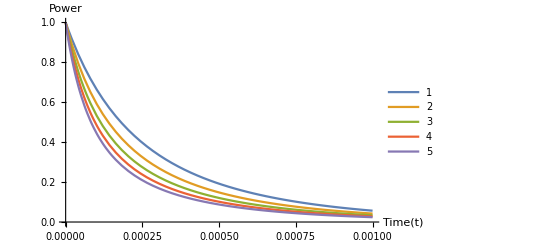

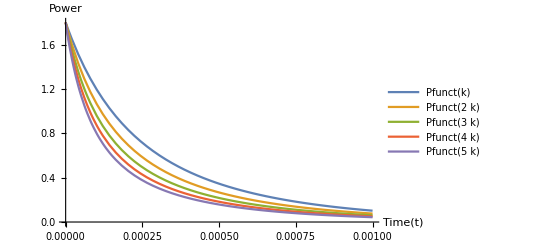

(ⅇ^(6250 t/3) (-5.39765×10^-65-1.80064×10^-43 ksub+6.5976×10^-20 ksub^2+ⅇ^(6250 t/3) (-4.9066×10^-65-3.59843×10^-42 ksub-6.5976×10^-20 ksub^2)))/((-1. ksub+ⅇ^(6250 t/3) (2.72708×10^-23+ksub))^3)

-(ⅇ^(6250 t/3) (-5.39765×10^-65-1.80064×10^-43 ksub+6.5976×10^-20 ksub^2+ⅇ^(6250 t/3) (-4.9066×10^-65-3.59843×10^-42 ksub-6.5976×10^-20 ksub^2)))/((-1. ksub+ⅇ^(6250 t/3) (2.72708×10^-23+ksub))^3)

-Graphics-

```mathematica
ClearAll["Global`*"]
Subscript[r, γ0]=(2 ksub Subscript[N, 0])/(Subscript[γ, 0] 𝕍);Subscript[r, γ]=(2 ksub Subscript[N, 2])/(Subscript[γ, 0] 𝕍);Subscript[γ, eff]=Subscript[γ, 0] (1+Subscript[r, γ]);Subscript[τ, eff]=1/Subscript[γ, eff];Subscript[γ, effP]=(1+2 Subscript[r, γ])/(1+Subscript[r, γ])Subscript[γ, eff];Subscript[τ, effP]=1/Subscript[γ, effP];
Subscript[N, 2]=Simplify[(Subscript[N, 0] ⅇ^(-Subscript[γ, 0] t))/(1+Subscript[r, γ0] (1-ⅇ^(-Subscript[γ, 0] t)))];Nfunct[ksub_]=Subscript[N, 2]; (* This line and the next are the crux of this cell *)
Pt=(Subscript[ℙ, 0] (Subscript[γ, 0] Subscript[N, 2]+(2 k Subscript[N, 2]^2)/𝕍))/(Subscript[γ, 0] Subscript[N, 0]+(2 k Subscript[N, 0]^2)/𝕍);Pfunct[ksub_]=Pt;
Subscript[N, 0]=3 10^14;Subscript[γ, 0]=1/(480/10^6);k=1.5/10^23;l=.1;r=5/10^6;area=π r^2;𝕍=area l;α=1.059;Subscript[k, corr]=7.844/10^23;Subscript[ℙ, 0]=1.8;
AttemptN=Plot[{Nfunct[k],Nfunct[Subscript[k, corr]]},{t,0,1.5 10^-3},AxesLabel->{"Time(t)","N_2"}, PlotLegends->{"Literature k","Corrected k"},Filling->Bottom]

AttemptP=Plot[{Pfunct[k],Pfunct[Subscript[k, corr]]},{t,0,1 10^-3},AxesLabel->{"Time(t)","Power"},PlotLegends->{"Power Decay w/ Lit k","Power Decay w/Corrected k"},Filling->Bottom]

Pdecay=Plot[{Pfunct[k]/Subscript[ℙ, 0],Pfunct[2 k]/Subscript[ℙ, 0],Pfunct[3 k]/Subscript[ℙ, 0],
Pfunct[4 k]/Subscript[ℙ, 0],Pfunct[5 k]/Subscript[ℙ, 0]},{t,0,1 10^-3},AxesLabel->{"Time(t)","Power"},PlotLegends->Automatic](* ratio version of AttemptP *)
Pdecay=Plot[{Pfunct[k],Pfunct[2 k],Pfunct[3 k],
Pfunct[4 k],Pfunct[5 k]},{t,0,1 10^-3},AxesLabel->{"Time(t)","Power"},PlotLegends->"Expressions"](* Difference in P ratio with changing k *)

dPt=Simplify[D[Pt,t]]
RatePfunct[ksub_]=-dPt (* you don't need this negative sign, it just makes the final graph look cleaner *)
PDecayRate=Plot[{RatePfunct[k],RatePfunct[2 k],RatePfunct[3 k],RatePfunct[4 k],
RatePfunct[5 k]},{t,0,.8 10^-3},AxesLabel->{"Time(t)","P_out Rate of Change"},
PlotLabels->Automatic](* Unlike others, this value will rise very quickly because of the nature of decay rate with higher k values *)
```

## Plotting τ_eff With Respect To Time

#### Organized Lifetime, N_2, k, and Power Comparisons

Near the end here we come to realize that in fact, N_2 itself is dependent on the value of k. Based on required equilibrium between the two sides of the rate equation discussed in the beginning, we decide to make a function that will automatically augment N_2 in accordance with updated or additional k values. We will keep it simple at the moment with only 2 different k values and 2 corresponding N_2 values. The first k value shown as k1 is from the literature (what we believe to be incorrect), and k2 is our assumed correct k value. N01 is our corresponding literature N_2, and N02 is our corrected version. Please don’t get N01 or N02 mixed up with N_0. Due to function limitations within Mathematica, we couldn’t use subscripts in certain areas of this upcoming cell.

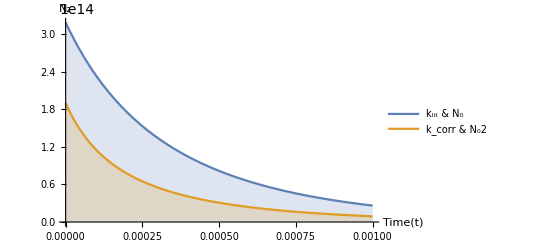

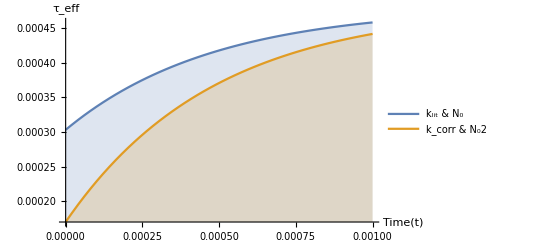

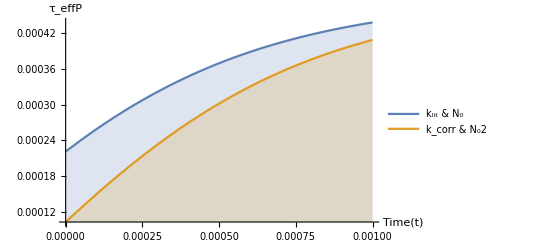

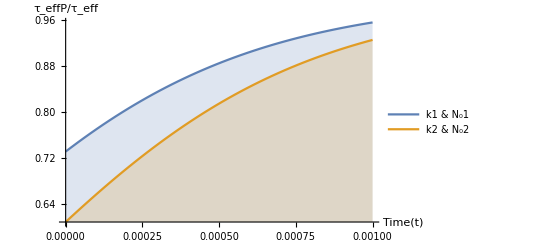

```mathematica
ClearAll["Global`*"]
Subscript[r, γ0]=(2 k N0)/(Subscript[γ, 0] 𝕍);Subscript[N, 2]=(N0 ⅇ^(-Subscript[γ, 0] t))/(1+Subscript[r, γ0] (1-ⅇ^(-Subscript[γ, 0] t)));N01=3.185/10^-14;N02=1.9/10^-14;k1=1.5/10^23;k2=7.844/10^23; (* Replaceables for Subscript[PlotN, 2] *)
Subscript[r, γ]=(2 k Subscript[N, 2])/(Subscript[γ, 0] 𝕍);Subscript[γ, eff]=Subscript[γ, 0] (1+Subscript[r, γ]);Subscript[τ, eff]=1/Subscript[γ, eff];Subscript[γ, effP]=(1+2 Subscript[r, γ])/(1+Subscript[r, γ])Subscript[γ, eff];Subscript[τ, effP]=1/Subscript[γ, effP]; (* Replaceables for τ Plots *)
Subscript[γ, 0]=1/(480 10^-6);l=.1;r=5/10^6;area=π r^2;𝕍=area l;α=1.059; (* Hard Variables *)

Subscript[PlotPrepN, 2][N0_,k_]=Subscript[N, 2];   Subscript[PlotPrepτ, eff][N0_,k_]=Subscript[τ, eff];   Subscript[PlotPrepτ, effP][N0_,k_]=Subscript[τ, effP];
(* Preparing expressions to be plotted below *)

Plot[{Subscript[PlotPrepN, 2][N01,k1],Subscript[PlotPrepN, 2][N02,k2]},{t,0,1 10^-3},AxesLabel->{"Time(t)","N_2"},PlotLegends->{"k_lit & N_0","k_corr & N_02"}, Filling->Bottom]
Plot[{Subscript[PlotPrepτ, eff][N01,k1],Subscript[PlotPrepτ, eff][N02,k2]},{t,0,10^-3},PlotLegends->{"k_lit & N_0","k_corr & N_02"},AxesLabel->{"Time(t)","τ_eff"},Filling->Bottom]
Plot[{Subscript[PlotPrepτ, effP][N01,k1],Subscript[PlotPrepτ, effP][N02,k2]},{t,0,10^-3},AxesLabel->{"Time(t)","τ_effP"},PlotLegends->{"k_lit & N_0","k_corr & N_02"},Filling->Bottom]
Plot[{(Subscript[PlotPrepτ, effP][N01,k1])/(Subscript[PlotPrepτ, eff][N01,k1]),(Subscript[PlotPrepτ, effP][N02,k2])/(Subscript[PlotPrepτ, eff][N02,k2])},{t,0,10^-3},PlotLegends->{"k1 & N_01","k2 & N_02"}, AxesLabel->{"Time(t)","τ_effP/τ_eff"},Filling->Bottom]
```

This last cell simply displays how quickly the luminescence output of the laser decays once the pump laser is turned off.

-(ⅇ^(t γ_0) ℙ_0 𝕍^2 γ_0^3 (2 (1+ⅇ^(t γ_0)) k N_0+ⅇ^(t γ_0) 𝕍 γ_0))/((2 (-1+ⅇ^(t γ_0)) k N_0+ⅇ^(t γ_0) 𝕍 γ_0)^3)

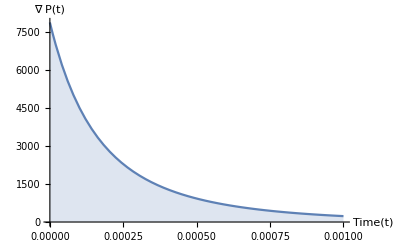

```mathematica
ClearAll["Global`*"]
Subscript[r, γ0]=(2 k Subscript[N, 0])/(Subscript[γ, 0] 𝕍);Subscript[r, γ]=(2 k Subscript[N, 2])/(Subscript[γ, 0] 𝕍);Subscript[γ, eff]=Subscript[γ, 0] (1+Subscript[r, γ]);Subscript[τ, eff]=1/Subscript[γ, eff];Subscript[γ, effP]=(1+2 Subscript[r, γ])/(1+Subscript[r, γ])Subscript[γ, eff];Subscript[τ, effP]=1/Subscript[γ, effP];
Subscript[N, 2]=Simplify[(Subscript[N, 0] ⅇ^(-Subscript[γ, 0] t))/(1+Subscript[r, γ0] (1-ⅇ^(-Subscript[γ, 0] t)))];
Nfunct[ksub_]=Subscript[N, 2];
Pt=(Subscript[ℙ, 0] (Subscript[γ, 0] Subscript[N, 2]+(2 k Subscript[N, 2]^2)/𝕍))/(Subscript[γ, 0] Subscript[N, 0]+(2 k Subscript[N, 0]^2)/𝕍);
dPt=Simplify[D[Pt,t]]
∇Pfunct[ksub_]=dPt;
Subscript[N, 0]=3 10^14;Subscript[γ, 0]=1/(480/10^6);k=1.5/10^23;l=.1;r=5/10^6;area=π r^2;𝕍=area l;α=1.059;Subscript[k, corr]=7.844/10^23;Subscript[ℙ, 0]=1.8;
dPt=-Simplify[D[Pt,t]];
Plot[dPt,{t,0,1 10^-3},AxesLabel->{"Time(t)","∇ P(t)"},Filling->Bottom]
```